```mathematica
ClearAll
```

ClearAll

```mathematica
Remove[Ucoefficient]
```

```mathematica
(*U Coefficient*)
Ucoefficient[n_]:=Ucoefficient[n]=2*x*Ucoefficient[n-1]-Ucoefficient[n-2];
Ucoefficient[0]=1;
Ucoefficient[1]=2x;
Simplify[Ucoefficient[10]];
```

```mathematica
(*?Ucoefficient*)
?Ucoefficient
```

```mathematica
k=5;
se=Total[Table[(-1)^i*b[i],{i,0,k}]]
Ak=Simplify[Total[Table[Ucoefficient[i]*(b[i]-b[i+1]),{i,0,k-1}]]+Ucoefficient[k]*b[k]]
```

b[0]-b[1]+b[2]-b[3]+b[4]-b[5]

b[0]+(-1+2 x) b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3]+b[4]+4 x b[4]-12 x^2 b[4]-8 x^3 b[4]+16 x^4 b[4]-b[5]+6 x b[5]+12 x^2 b[5]-32 x^3 b[5]-16 x^4 b[5]+32 x^5 b[5]

```mathematica
2 x-2 x (-1+4 x^2)+2 x (1-4 x^2+2 x (-2 x+2 x (-1+4 x^2)))
```

2 x-2 x (-1+4 x^2)+2 x (1-4 x^2+2 x (-2 x+2 x (-1+4 x^2)))

```mathematica
Simplify[2 x-2 x (-1+4 x^2)+2 x (1-4 x^2+2 x (-2 x+2 x (-1+4 x^2)))]
```

6 x-32 x^3+32 x^5

```mathematica
Simplify[b[0]-b[1]+2 x b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3]+b[4]+4 x b[4]-12 x^2 b[4]-8 x^3 b[4]+16 x^4 b[4]]
```

b[0]+(-1+2 x) b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3]+b[4]+4 x b[4]-12 x^2 b[4]-8 x^3 b[4]+16 x^4 b[4]

```mathematica
D[Ak, x]
```

2 b[1]-2 b[2]+8 x b[2]-4 b[3]-8 x b[3]+24 x^2 b[3]+4 b[4]-24 x b[4]-24 x^2 b[4]+64 x^3 b[4]+6 b[5]+24 x b[5]-96 x^2 b[5]-64 x^3 b[5]+160 x^4 b[5]-6 b[6]+48 x b[6]+96 x^2 b[6]-320 x^3 b[6]-160 x^4 b[6]+384 x^5 b[6]-8 b[7]-48 x b[7]+240 x^2 b[7]+320 x^3 b[7]-960 x^4 b[7]-384 x^5 b[7]+896 x^6 b[7]

```mathematica
Expand[Ak]
```

b[0]-b[1]+2 x b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3]

```mathematica
Expand[Ak]
```

b[0]-b[1]+2 x b[1]-b[2]-2 x b[2]+4 x^2 b[2]

```mathematica
FullSimplify[Ak]
```

b[0]-b[2]+(-1+2 x) (b[1]+2 x b[2])

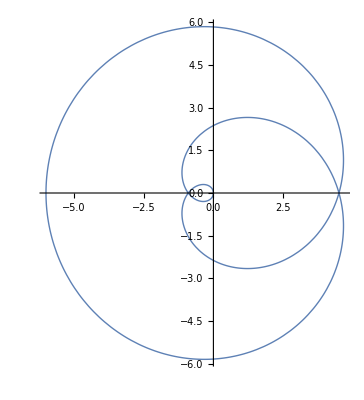

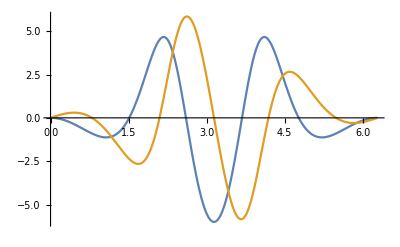

```mathematica
Minimize[{se,b[0]-b[1]+2 x (b[1]-b[2])+(-1+4 x^2) b[2]==0&&b[0]+b[1]+b[2]==1&&D[Ak,x]==0},{b[0],b[1],b[2],x}];
Ak2p1= (ⅇ^(3 ⅈ ξ)-ⅇ^(2ⅈ ξ))/(5/9 ⅇ^(2ⅈ ξ) +1/3 ⅇ^(ⅈ ξ) +1/9);
ParametricPlot[{Re[Ak2p1],Im[Ak2p1]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All]
Plot[{Re[Ak2p1],Im[Ak2p1]},{ξ,0,2π},PlotRange->All]
(* k=2 p=1 2n偶数*)
```

```mathematica
b[0]+(-1+2 x) b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3];
D[b[0]+(-1+2 x) b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3],x]
(* k=3 p=1 2n-1奇数*)
```

2 b[1]-2 b[2]+8 x b[2]-4 b[3]-8 x b[3]+24 x^2 b[3]

```mathematica
Simplify[2 b[1]-2 b[2]+8 x b[2]-4 b[3]-8 x b[3]+24 x^2 b[3]]
```

2 (b[1]+(-1+4 x) b[2]+2 (-1-2 x+6 x^2) b[3])

```mathematica
Minimize[{b[0]-b[1]+b[2]-b[3],
b[0]+b[1]+b[2]+b[3]==1&&b[0]+(-1+2 x) b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3]==0&&
2 (b[1]+(-1+4 x) b[2]+2 (-1-2 x+6 x^2) b[3])==0&&
b[0]-3 b[1]-b[2]+2  b[2]+4  b[2]+b[3]+4  b[3]-4  b[3]-8 b[3]==0},{b[0],b[1],b[2],b[3],x}]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{b[0]→Indeterminate,b[1]→Indeterminate,b[2]→Indeterminate,b[3]→Indeterminate,x→Indeterminate}}

```mathematica
Solve[{b[0]+b[1]+b[2]+b[3]+b[4]==1,b[0]+(-1+2 x) b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3]+b[4]+4 x b[4]-12 x^2 b[4]-8 x^3 b[4]+16 x^4 b[4]==0,b[0]+(-1+2 y) b[1]-b[2]-2 y b[2]+4 y^2 b[2]+b[3]-4 y b[3]-4 y^2 b[3]+8 y^3 b[3]+b[4]+4 y b[4]-12 y^2 b[4]-8 y^3 b[4]+16 y^4 b[4]==0,2 b[1]-2 b[2]+8 x b[2]-4 b[3]-8 x b[3]+24 x^2 b[3]+4 b[4]-24 x b[4]-24 x^2 b[4]+64 x^3 b[4]==0,2 b[1]-2 b[2]+8 y b[2]-4 b[3]-8 y b[3]+24 y^2 b[3]+4 b[4]-24 y b[4]-24 y^2 b[4]+64 y^3 b[4]==0},{b[0],b[1],b[2],b[3],b[4],y,x}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b[0]→1/(2 (-1+y)^2)(1-2 y+2 y^2-2 b[3]+4 y b[3]-10 y^2 b[3]+16 y^3 b[3]-8 y^4 b[3]-2 b[4]+4 y b[4]-10 y^2 b[4]-16 y^3 b[4]+56 y^4 b[4]-32 y^5 b[4]),b[1]→1/(4 (-1+y)^2)(1-4 y+4 b[3]+8 y b[3]-12 y^2 b[3]-16 y^3 b[3]+16 y^4 b[3]-4 b[4]+24 y b[4]+28 y^2 b[4]-48 y^3 b[4]-64 y^4 b[4]+64 y^5 b[4]),b[2]→(1-4 b[3]-8 y b[3]+28 y^2 b[3]-16 y^3 b[3]+4 b[4]-24 y b[4]-12 y^2 b[4]+80 y^3 b[4]-48 y^4 b[4])/(4 (-1+y)^2),x→y},{b[0]→1-5/(8 (-1+x)^2 (-1+y)^2)+(5 x)/(4 (-1+x)^2 (-1+y)^2)-x^2/(2 (-1+x)^2 (-1+y)^2)+(5 y)/(4 (-1+x)^2 (-1+y)^2)-(2 x y)/((-1+x)^2 (-1+y)^2)+(x^2 y)/((-1+x)^2 (-1+y)^2)-y^2/(2 (-1+x)^2 (-1+y)^2)+(x y^2)/((-1+x)^2 (-1+y)^2),b[1]→1/(4 (-1+x)^2 (-1+y)^2)-(3 x)/(4 (-1+x)^2 (-1+y)^2)+x^2/(4 (-1+x)^2 (-1+y)^2)-(3 y)/(4 (-1+x)^2 (-1+y)^2)+(x y)/((-1+x)^2 (-1+y)^2)-(x^2 y)/((-1+x)^2 (-1+y)^2)+y^2/(4 (-1+x)^2 (-1+y)^2)-(x y^2)/((-1+x)^2 (-1+y)^2),b[2]→1/(4 (-1+x)^2 (-1+y)^2)-x/(4 (-1+x)^2 (-1+y)^2)+x^2/(4 (-1+x)^2 (-1+y)^2)-y/(4 (-1+x)^2 (-1+y)^2)+(x y)/((-1+x)^2 (-1+y)^2)+y^2/(4 (-1+x)^2 (-1+y)^2),b[3]→1/(16 (-1+x)^2 (-1+y)^2)-x/(4 (-1+x)^2 (-1+y)^2)-y/(4 (-1+x)^2 (-1+y)^2),b[4]→1/(16 (-1+x)^2 (-1+y)^2)}}

```mathematica
Minimize[{b[0]-b[1]+b[2]-b[3]+b[4],
b[0]+b[1]+b[2]+b[3]+b[4]==1&&b[0]+(-1+2 x) b[1]-b[2]-2 x b[2]+4 x^2 b[2]+b[3]-4 x b[3]-4 x^2 b[3]+8 x^3 b[3]+b[4]+4 x b[4]-12 x^2 b[4]-8 x^3 b[4]+16 x^4 b[4]==0&&b[0]+(-1+2 y) b[1]-b[2]-2 y b[2]+4 y^2 b[2]+b[3]-4 y b[3]-4 y^2 b[3]+8 y^3 b[3]+b[4]+4 y b[4]-12 y^2 b[4]-8 y^3 b[4]+16 y^4 b[4]==0&&2 b[1]-2 b[2]+8 x b[2]-4 b[3]-8 x b[3]+24 x^2 b[3]+4 b[4]-24 x b[4]-24 x^2 b[4]+64 x^3 b[4]==0&&2 b[1]-2 b[2]+8 y b[2]-4 b[3]-8 y b[3]+24 y^2 b[3]+4 b[4]-24 y b[4]-24 y^2 b[4]+64 y^3 b[4]==0},{b[0],b[1],b[2],b[3],b[4],x,y}]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{b[0]→Indeterminate,b[1]→Indeterminate,b[2]→Indeterminate,b[3]→Indeterminate,b[4]→Indeterminate,x→Indeterminate,y→Indeterminate}}